```mathematica
SetDirectory[NotebookDirectory[]]
data = Import["output.csv"]
```

/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155

{{Time / ns,TotEng / Kcal mole⁻.b9,KinEng / Kcal mole⁻.b9,PotEng / Kcal mole⁻.b9,Enthalpy / Kcal mole⁻.b9,Temp / K,Press / atm,Volume / Å.b3,Density / g cm⁻.b9},{0.,1.0822×10^6,0.,1.0822×10^6,2.68199×10^6,0.,1.18788×10^6,92345.4,0.977597},{0.005,-33681.3,0.,-33681.3,-35123.9,0.,-1071.11,92345.4,0.977597},29998,{150.115,-33527.9,1409.51,-34937.4,-34090.9,156.628,-418.066,92345.4,0.977597},{150.12,-33558.7,1375.93,-34934.7,-34045.2,152.897,-361.219,92345.4,0.977597},{150.125,-33564.7,1387.,-34951.7,-34183.7,154.127,-459.635,92345.4,0.977597}}
 |  |  |  |

```mathematica
blue = RGBColor[21/256,109/256,204/256];
red = RGBColor[255/256,64/256,49/256];
green = RGBColor[0/256,163/256,55/256];
yellow = RGBColor[1.,0.62,0.19];
purple = RGBColor[1.,0.89,0.81];
purple = RGBColor[0.62,0.63,1.];
```

```mathematica
t = Transpose[data][[1]];
te = Transpose[data][[2]];
ke = Transpose[data][[3]];
pe = Transpose[data][[4]];
en = Transpose[data][[5]];
tp = Transpose[data][[6]];
pr = Transpose[data][[7]];
vo = Transpose[data][[8]];
de = Transpose[data][[9]];
```

```mathematica
rte = Partition[Riffle[t, te], 2];
rke = Partition[Riffle[t, ke], 2];
rpe = Partition[Riffle[t, pe], 2];
ren = Partition[Riffle[t, en], 2];
rtp = Partition[Riffle[t, tp], 2];
rpr = Partition[Riffle[t, pr], 2];
rvo = Partition[Riffle[t, vo], 2];
rde = Partition[Riffle[t, de], 2];
```

```mathematica
marte = MovingAverage[Rest[rte], 1000];
marke = MovingAverage[Rest[rke], 1000];
marpe = MovingAverage[Rest[rpe], 1000];
maren = MovingAverage[Rest[ren], 1000];
martp = MovingAverage[Rest[rtp], 1000];
marpr = MovingAverage[Rest[rpr], 1000];
marvo = MovingAverage[Rest[rvo], 1000];
marde = MovingAverage[Rest[rde], 1000];
```

```mathematica
rtempte = Partition[Riffle[tp, te], 2];
rtempke = Partition[Riffle[tp, ke], 2];
rtemppe = Partition[Riffle[tp, pe], 2];
rtempen = Partition[Riffle[tp, en], 2];
rtemppr = Partition[Riffle[tp, pr], 2];
rtempvo = Partition[Riffle[tp, vo], 2];
rtempde = Partition[Riffle[tp, de], 2];
```

```mathematica
martempte = MovingAverage[Rest[rtempte], 1000];
martempke = MovingAverage[Rest[rtempke], 1000];
martemppe = MovingAverage[Rest[rtemppe], 1000];
martempen= MovingAverage[Rest[rtempen], 1000];
martemppr = MovingAverage[Rest[rtemppr], 1000];
martempvo = MovingAverage[Rest[rtempvo], 1000];
martempde = MovingAverage[Rest[rtempde], 1000];
```

## Temp

## Raw data Temp

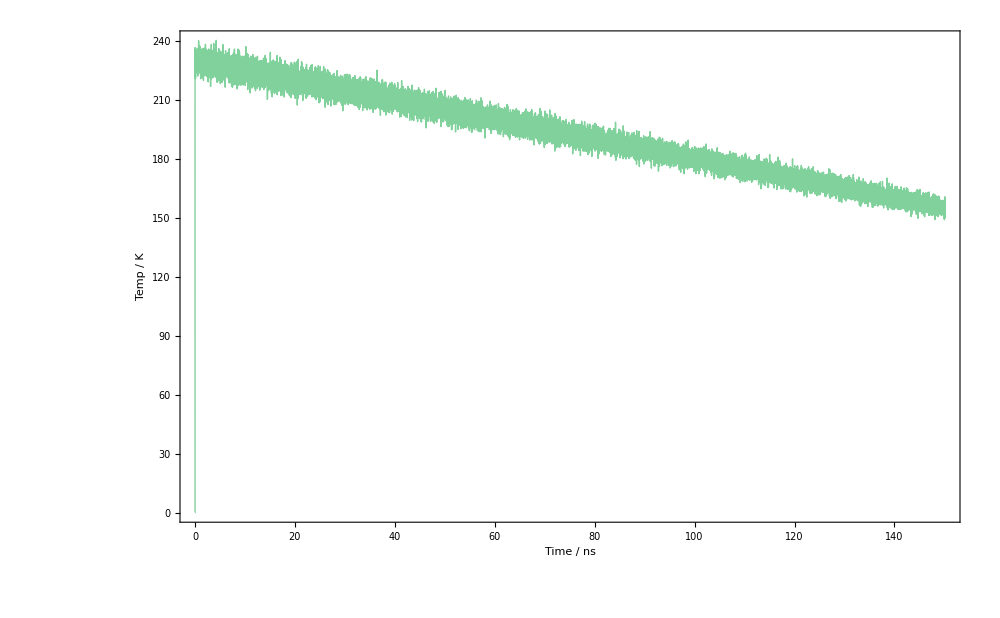

/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/raw-temp.svg

```mathematica
ListPlot[
rtp,
Joined->True,
FrameLabel->{"Time / ns", "Temp / K"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700}
]

Export["/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/raw-temp.svg",%]
```

## Moving average temp

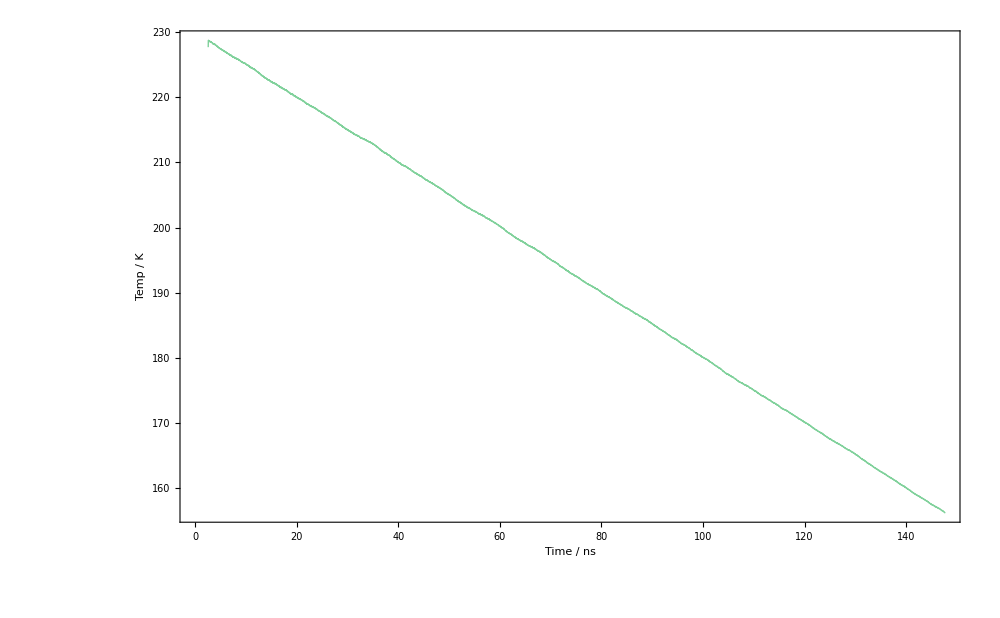

/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/temp.svg

```mathematica
ListPlot[
martp,
Joined->True,
FrameLabel->{"Time / ns", "Temp / K"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700}
]
Export["/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/temp.svg",%]
```

## Moving average temp from 50 -> 80ns

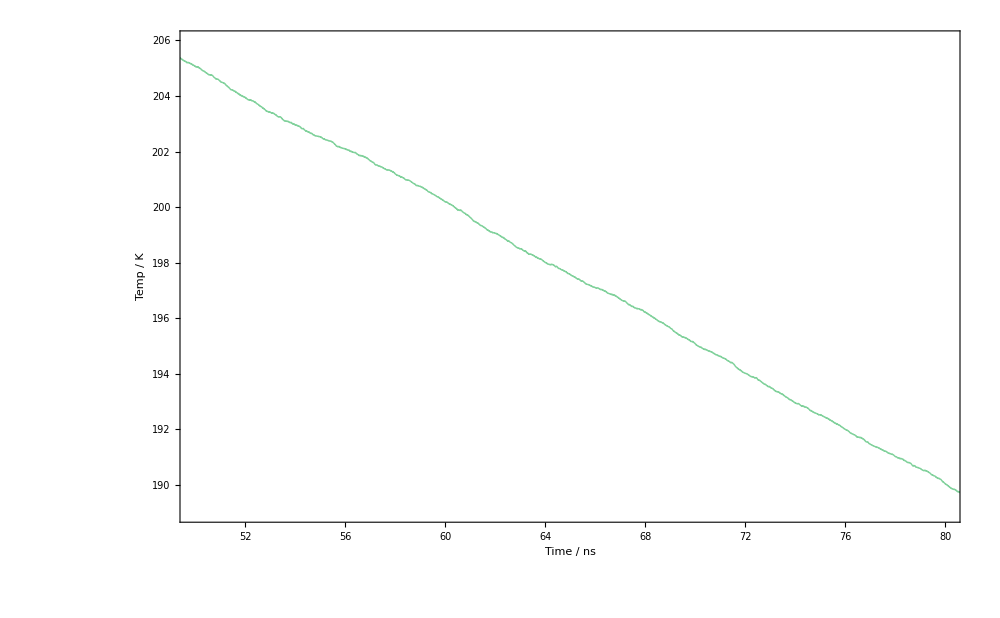

-Graphics-

```mathematica
ListPlot[
martp,
Joined->True,
FrameLabel->{"Time / ns", "Temp / K"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700},
PlotRange->{{50, 80}, {189, 206}}
]
```

## Pressure

## Raw data Press

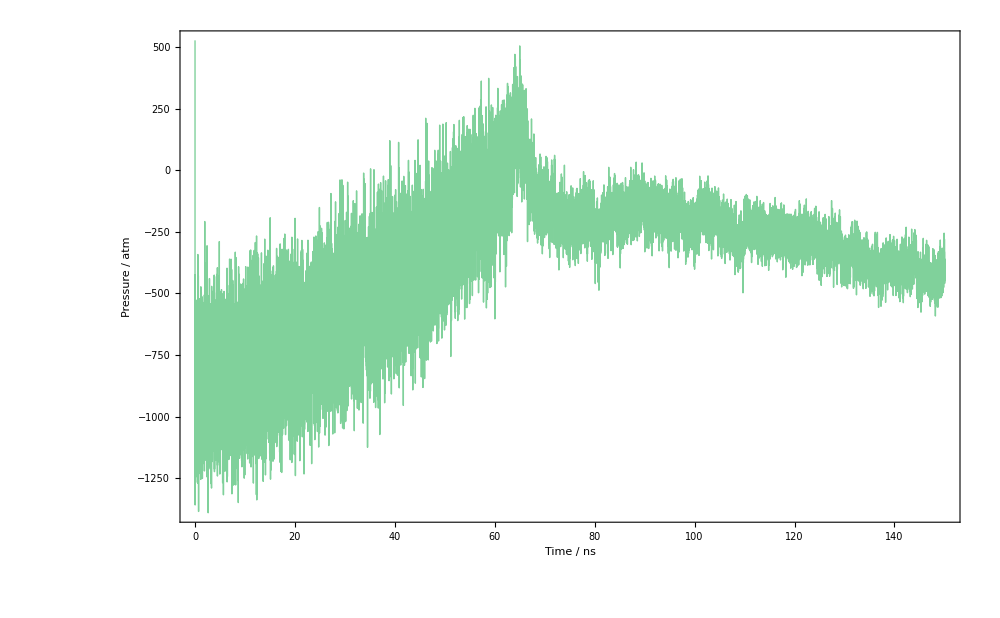

/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/raw-press.svg

```mathematica
ListPlot[
rpr,
Joined->True,
FrameLabel->{"Time / ns", "Pressure / atm"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700}
]

Export["/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/raw-press.svg",%]
```

## Raw Pressure vs Temp

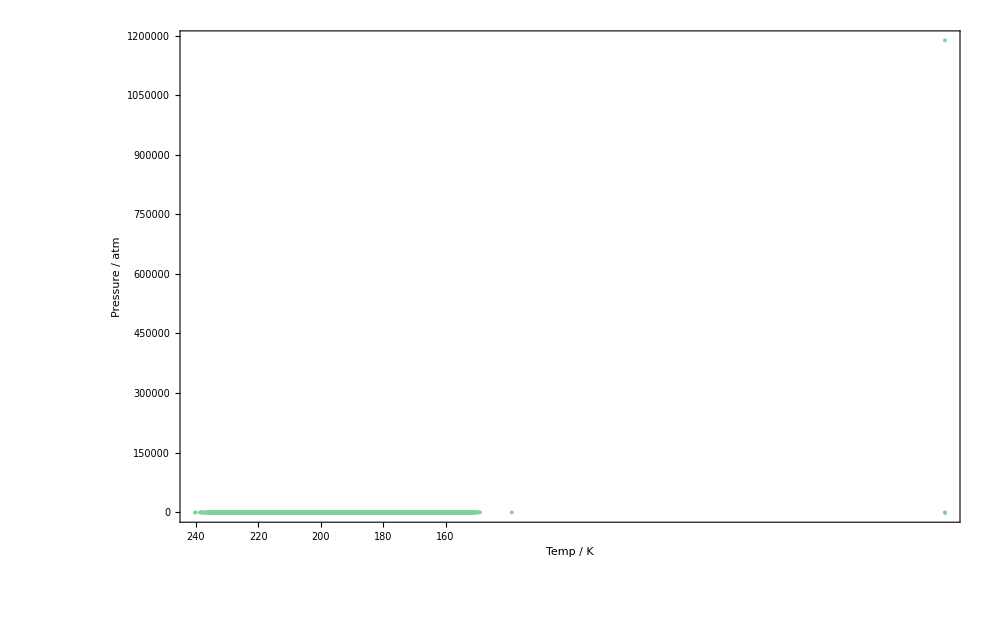

/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/raw-temp-press.svg

```mathematica
ListPlot[
rtemppr,
FrameLabel->{"Temp / K", "Pressure / atm"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700},
PlotRange->{{150, 240}, Automatic},ScalingFunctions->{"Reverse",Identity}
]
Export["/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/raw-temp-press.svg",%]
```

## Moving average Pressure vs Temp

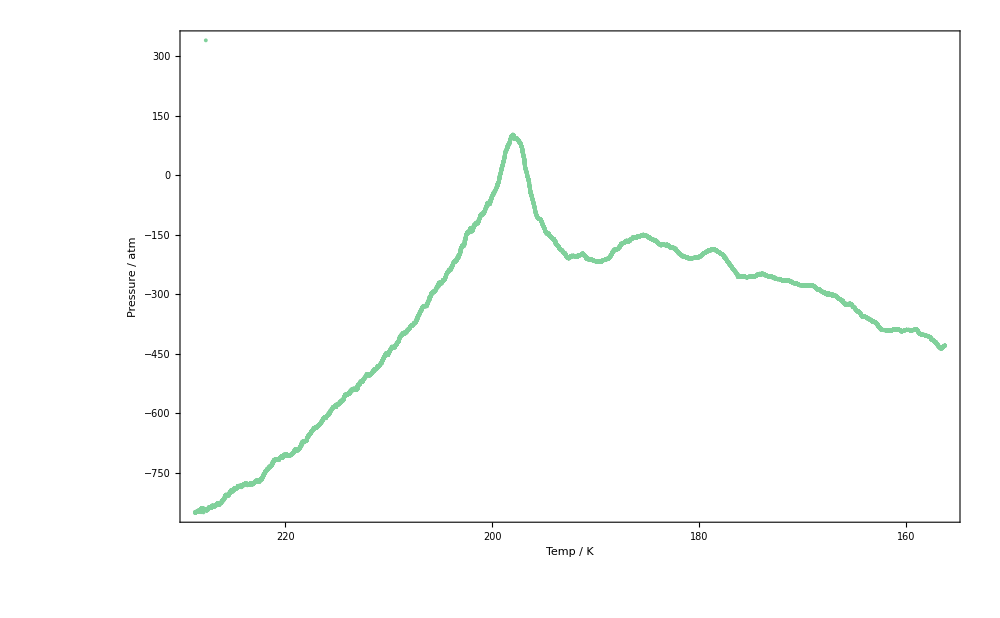

/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/temp-press.svg

```mathematica
ListPlot[
martemppr,
FrameLabel->{"Temp / K", "Pressure / atm"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700},
PlotRange->{{150, 240}, Automatic},ScalingFunctions->{"Reverse",Identity}
]
Export["/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/temp-press.svg",%]
```

## Moving average Press vs time

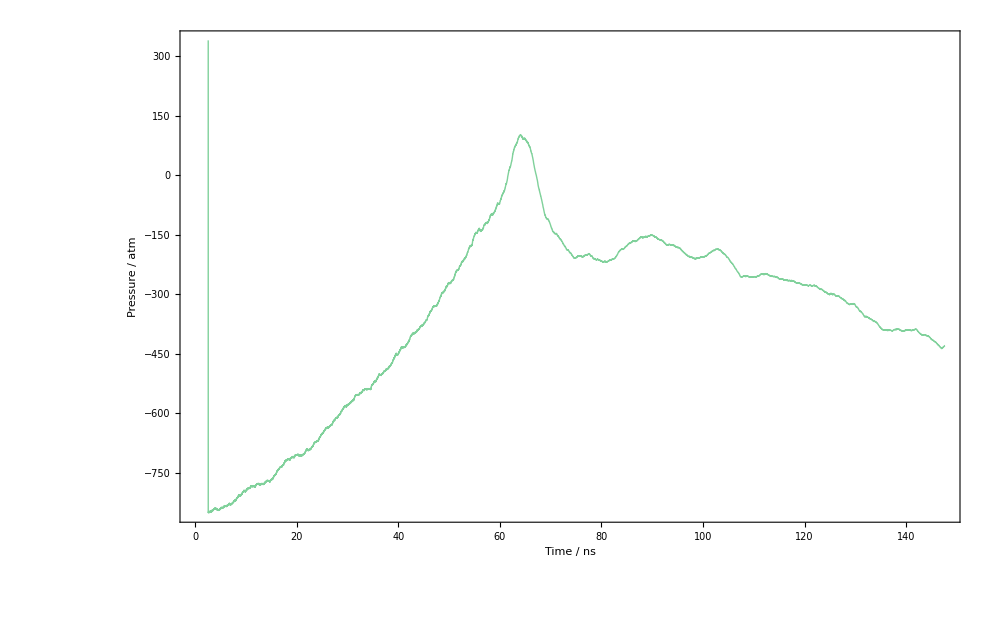

/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/press.svg

```mathematica
ListPlot[
marpr,
Joined->True,
FrameLabel->{"Time / ns", "Pressure / atm"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700}
]

Export["/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/press.svg",%]
```

## Moving average Press between 50 -> 80 ns

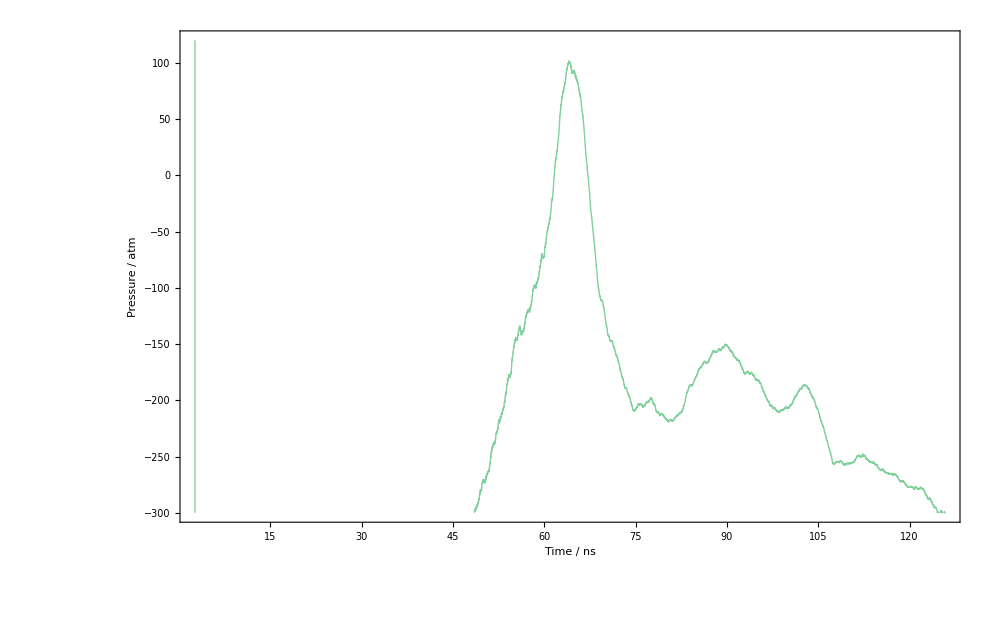

/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/press-50-80ns.svg

```mathematica
ListPlot[
marpr,
Joined->True,
FrameLabel->{"Time / ns", "Pressure / atm"}, 
Frame->{{True, None}, {True, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700},
PlotRange->{{50, 80}, {120, -300}}
]

Export["/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/press-50-80ns.svg",%]
```

## Energies

## Moving averages of TE, KE, PE, EN v time

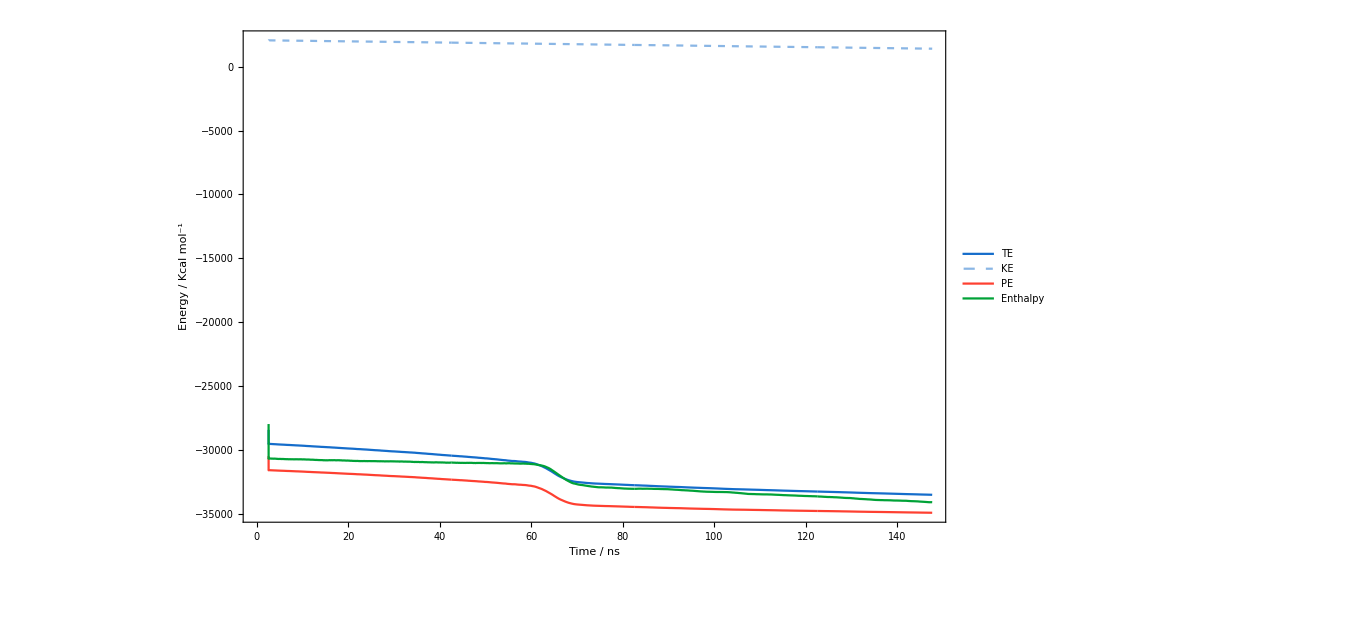

/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/energies.svg

```mathematica
ListPlot[
{ marte, marke, marpe, maren}, 
Joined->True,
FrameLabel->{"Time / ns", "Energy / Kcal mol^-1"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> 
{
{Thick,blue}, 

{Thick,Dashed,Lighter[blue,0.5]}, 

{Thick,red}, 

{Thick,green}
},
PlotLegends->{"TE", "KE", "PE", "Enthalpy"},
ImageSize -> {1000,700}
]
Export["/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/energies.svg",%]
```

## Moving averages of TE, KE, PE, EN v temp

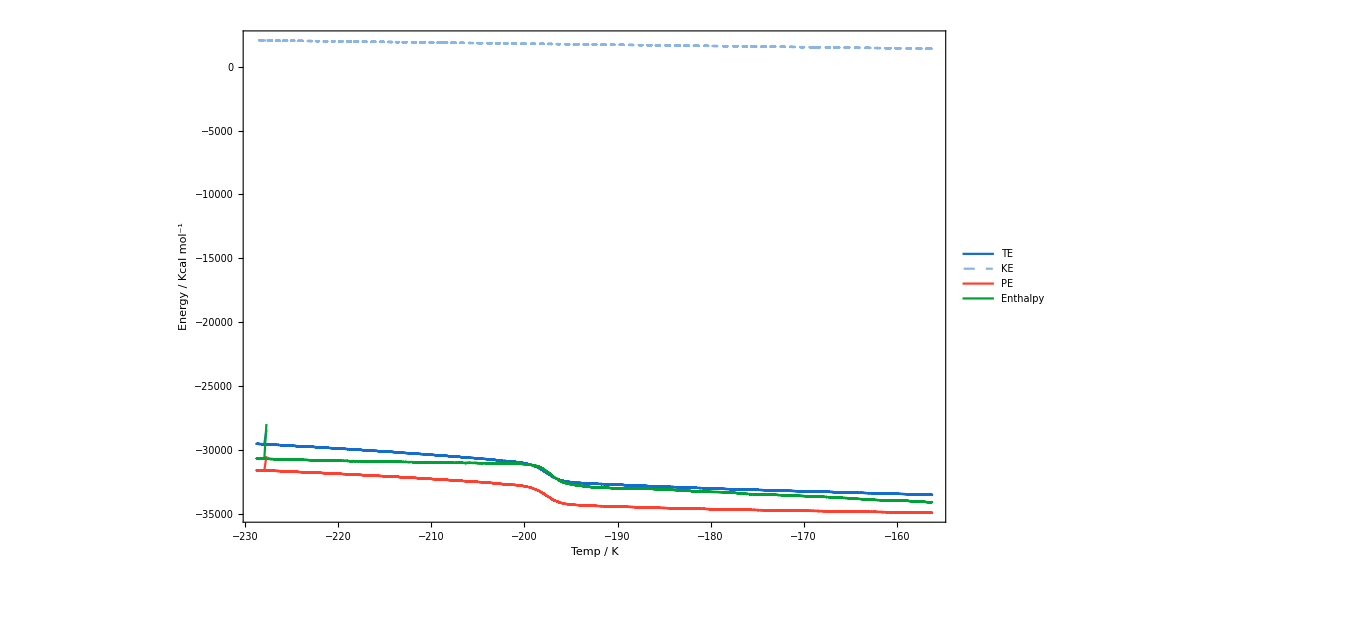

/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/temp-energies.svg

```mathematica
ListPlot[
{ martempte, martempke, martemppe, martempen}, 
Joined->True,
FrameLabel->{"Temp / K", "Energy / Kcal mol^-1"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> 
{
{Thick,blue}, 

{Thick,Dashed,Lighter[blue,0.5]}, 

{Thick,red}, 

{Thick,green}
},
PlotLegends->{"TE", "KE", "PE", "Enthalpy"},
ImageSize -> {1000,700},
ScalingFunctions->{"Reverse",Identity}
]
Export["/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/temp-energies.svg",%]
```

## Moving averages of TE, Enthalpy, PE

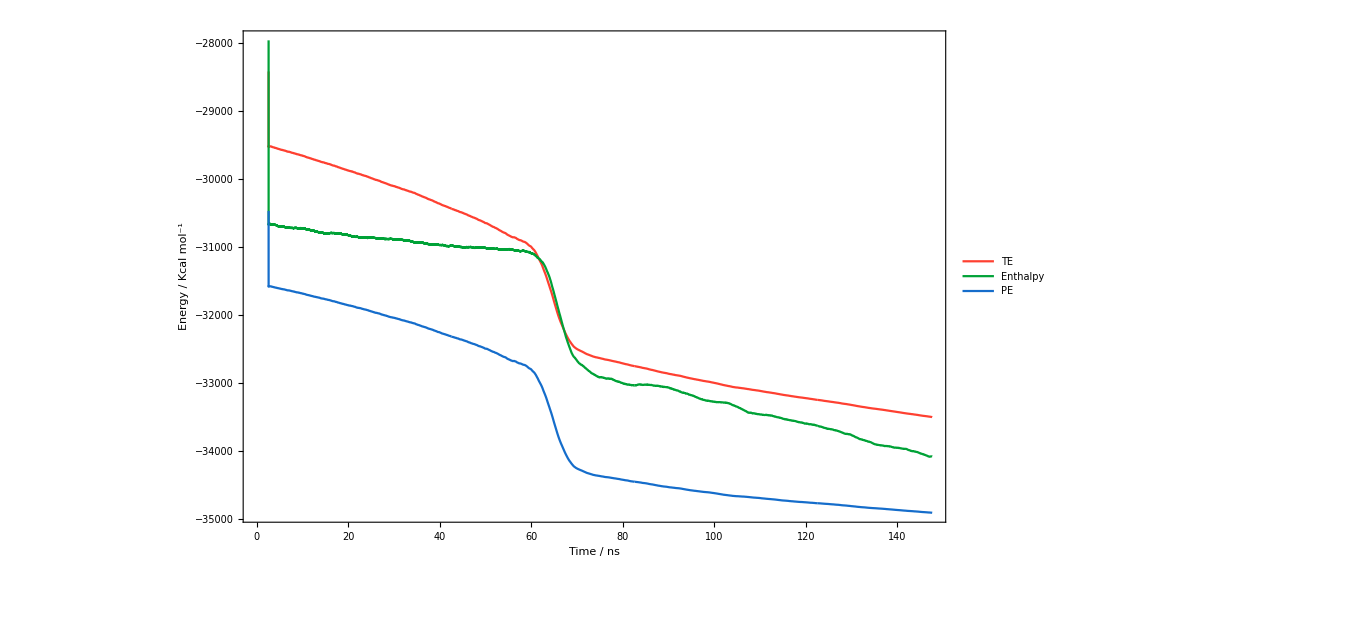

```mathematica
ListPlot[
{ marte, maren, marpe}, 
Joined->True,
FrameLabel->{"Time / ns", "Energy / Kcal mol^-1"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> 
{
{Thick,red}, 

{Thick,green},
{Thick, blue}
},
PlotLegends->{"TE","Enthalpy", "PE"},
ImageSize -> {1000,700}
]
```

## Moving averages of Enthalpy, PE vs Temp

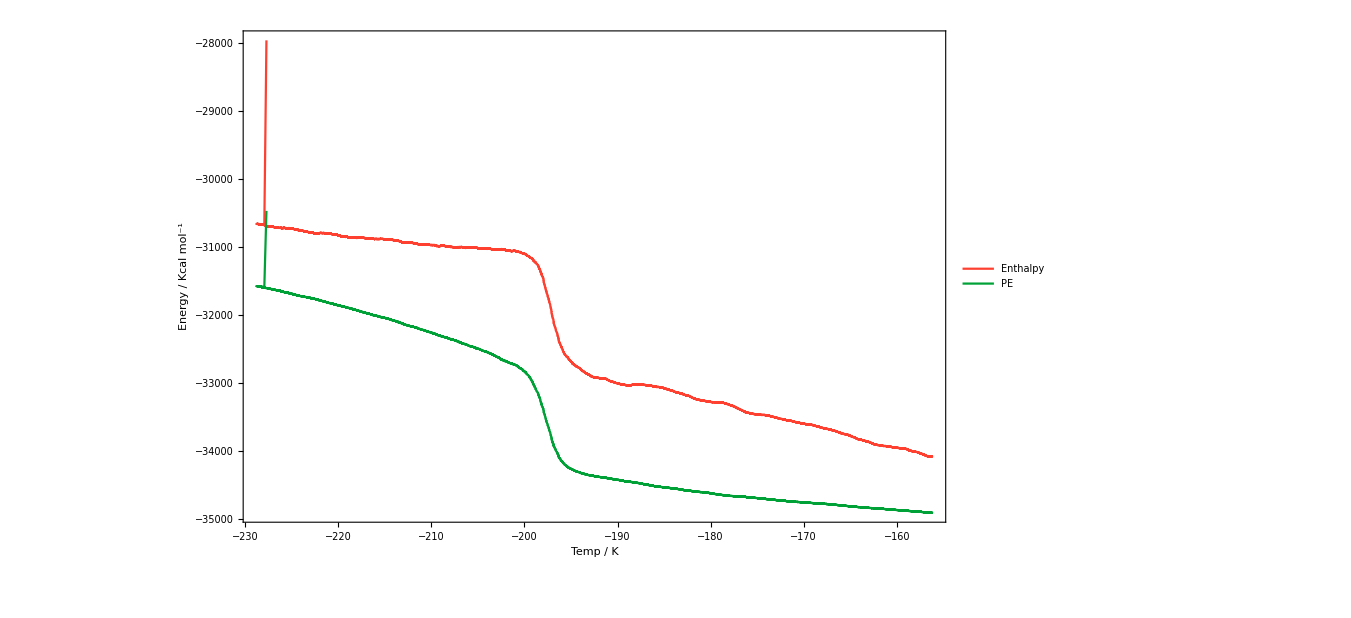

/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/temp-en-pe.svg

```mathematica
ListPlot[
{martempen, martemppe}, 
Joined->True,
FrameLabel->{"Temp / K", "Energy / Kcal mol^-1"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> 
{
{Thick,red}, 

{Thick,green}
},
PlotLegends->{"Enthalpy", "PE"},
ImageSize -> {1000,700},
ScalingFunctions->{"Reverse",Identity}
]
Export["/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/temp-en-pe.svg",%]
```

## Moving averages of TE, Enthalpy, PE from 205 -> 190K

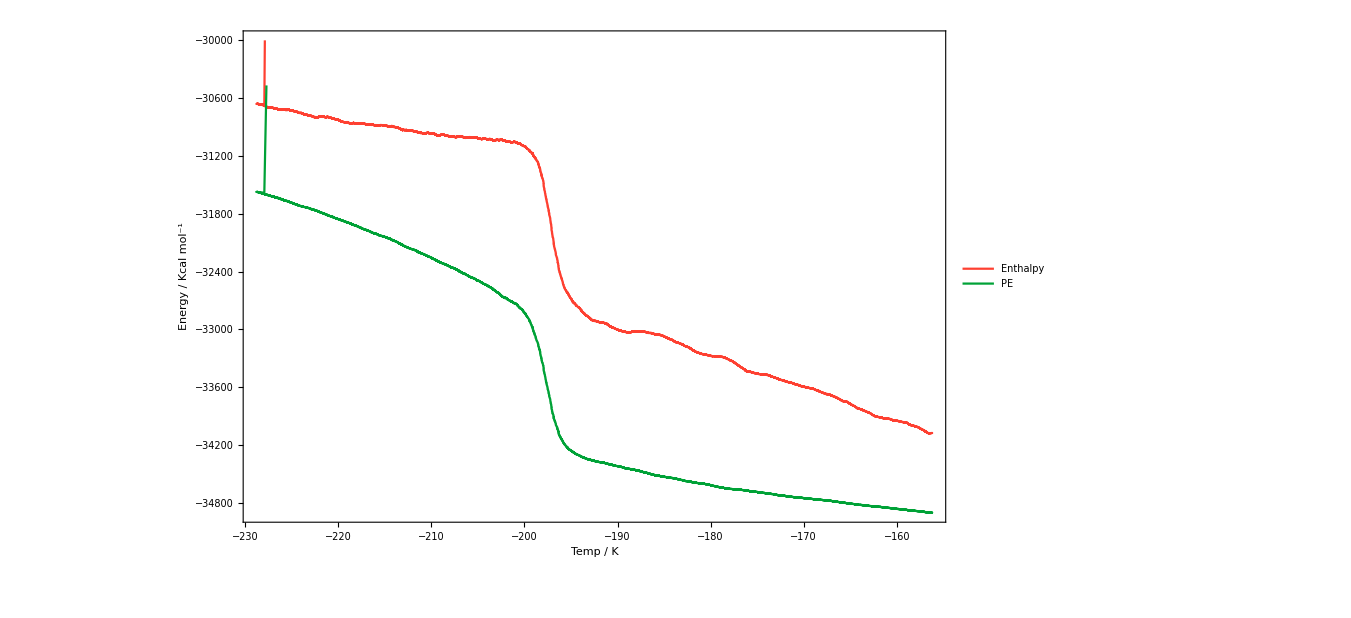

/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/temp-en-pe-205-190K.svg

```mathematica
ListPlot[
{martempen, martemppe}, 
Joined->True,
FrameLabel->{"Temp / K", "Energy / Kcal mol^-1"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> 
{
{Thick,red}, 

{Thick,green}
},
PlotLegends->{"Enthalpy", "PE"},
ImageSize -> {1000,700},
ScalingFunctions->{"Reverse",Identity},
PlotRange->{{205, 190}, {-30000, -35000}}
]
Export["/Users/haykkhachatryan/GoogleDrive/Programming/PHAS0052/MDavies+CH4/230-155/Plots/temp-en-pe-205-190K.svg",%]
```

## Combinations

## Enthalpy + Press form 50 -> 80 ns

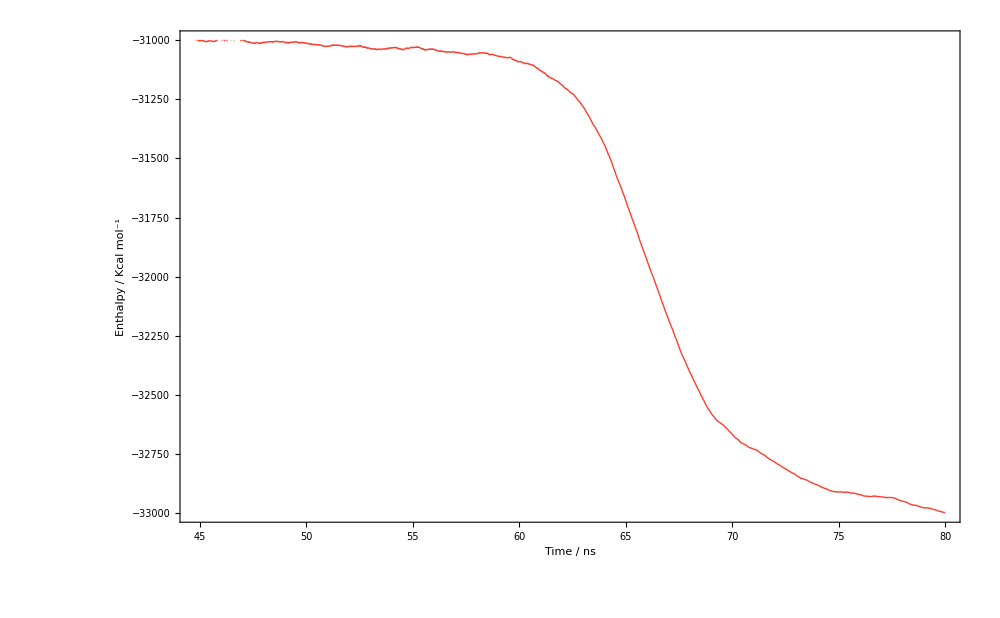
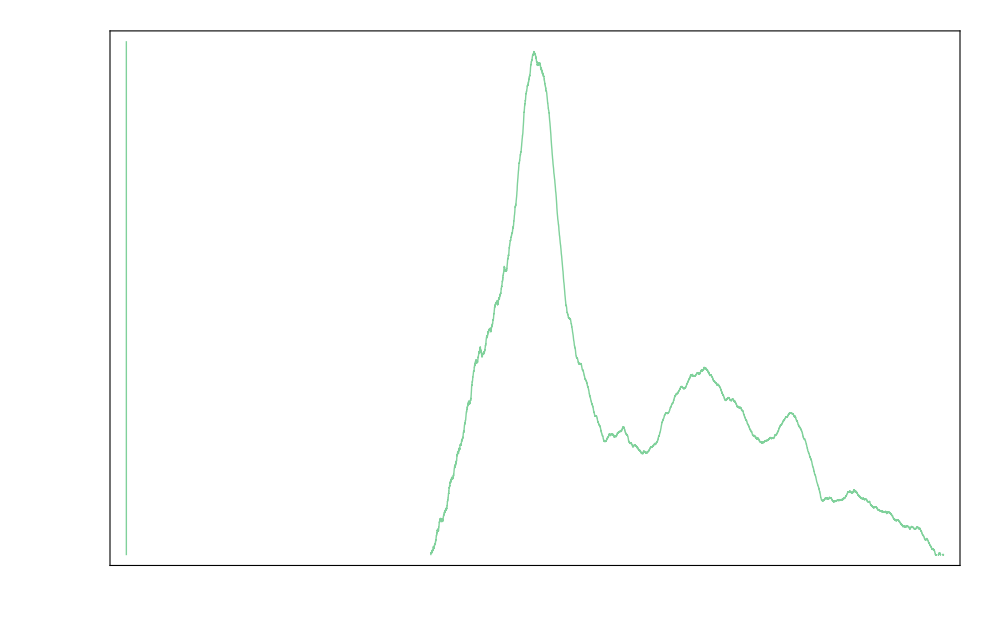

```mathematica
en130145 = ListPlot[
maren, 
Joined->True,
FrameLabel->{"Time / ns", "Enthalpy / Kcal mol^-1"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> {Thick,red},
ImageSize -> {1000,700},
PlotRange->{{50, 80}, {-31000, -33000}},
ImagePadding->110,
Frame->{True,True,True,False},
FrameTicks->{All, All, All, None},
FrameStyle->{Automatic,red,Automatic,Automatic}
];
p130145 = ListPlot[
marpr,
Joined->True,
FrameLabel->{{None, "Pressure / atm"}, {None, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700},
PlotRange->{{50, 80}, {110, -300}},
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,None}},
FrameStyle->{Automatic,Automatic,Automatic,green},
ImagePadding->110
];
Overlay[{en130145, p130145}]
```

## Enthalpy + Temp from 130 -> 145ns

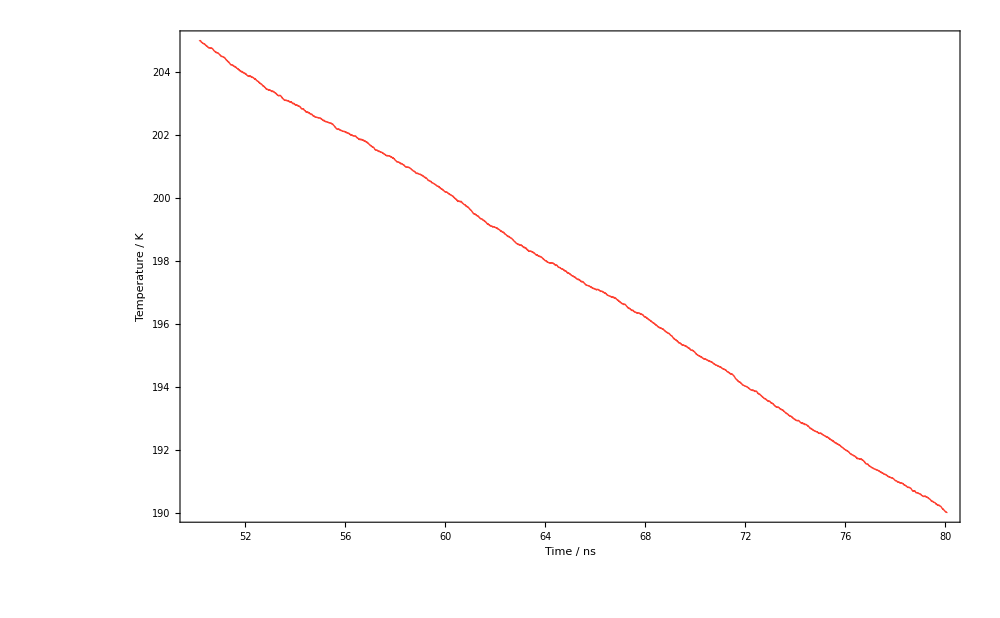
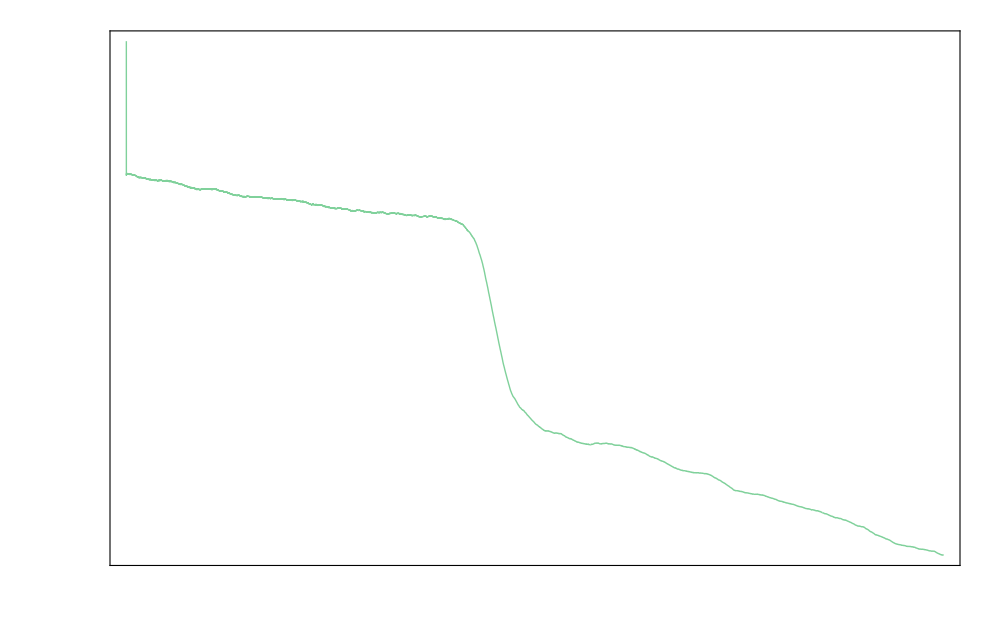

```mathematica
tp130145 = ListPlot[
martp, 
Joined->True,
FrameLabel->{"Time / ns", "Temperature / K"}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}},
PlotStyle-> {Thick,red},
ImageSize -> {1000,700},
PlotRange->{{50, 80}, {190, 205}},
ImagePadding->110,
Frame->{True,True,True,False},
FrameTicks->{All, All, All, None},
FrameStyle->{Automatic,red,Automatic,Automatic}
];
p130145 = ListPlot[
maren,
Joined->True,
FrameLabel->{{None, "Enthalpy / Kcal mol^-1"}, {None, None}}, 
LabelStyle->{Black, 20, FontFamily->"Latin Modern Roman"},
PlotStyle-> {Thick,Lighter[green, 0.5]},
ImageSize -> {1000,700},
PlotRange->{{50, 80}, {-29500, -34000}},
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,None}},
FrameStyle->{Automatic,Automatic,Automatic,green},
ImagePadding->110
];
Overlay[{tp130145, p130145}]
```